```mathematica
SetDirectory[FileNameJoin[{ParentDirectory@NotebookDirectory[], "data"}]]
```

/Users/arsenytokarev/Desktop/CourseWorks/Gas Dynamics/Code/data

```mathematica
NormalRepresentation[data_List]:= Module[
{solution, mesh},
solution = {ToExpression@#⟦1⟧, #⟦2⟧} &/@ data;
For[i =1, i <= Length@solution, ++i,
 solution⟦i,2⟧ = {ToExpression@#⟦1⟧, ToExpression@#⟦2⟧} &/@ solution⟦i,2⟧
];
Return@solution
];
```

```mathematica
Plots[data_List]:= ListLinePlot[#⟦2⟧ &/@ data, PlotRange->All]
```

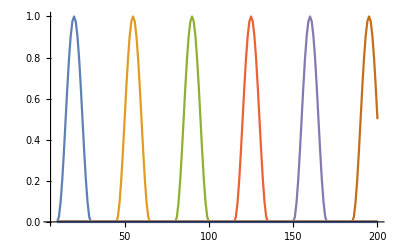

```mathematica
advection = NormalRepresentation@Import["advection.json"] ;
Plots[advection]
```

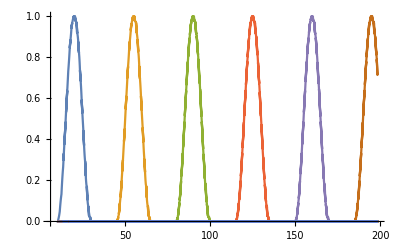

```mathematica
advectionPPM = NormalRepresentation@Import["advectionPPM.json"] ;
Plots[advectionPPM]
```